# QMC Lookup Table Analysis

This mathematica notebook is a re-writing of the old mathematica notebook that analyzes our data to fit the temperature.

## Introduction

## Fundamental Constants

## Settings and Helper Functions

```mathematica
co={RGBColor[0,0.4470,0.7410],
RGBColor[0.8500, 0.3250, 0.0980],
RGBColor[0.9290, 0.6940, 0.1250],
RGBColor[0.4940, 0.1840, 0.5560],
RGBColor[0.4660, 0.6740, 0.1880],
RGBColor[0.3010, 0.7450, 0.9330],
RGBColor[0.6350, 0.0780, 0.1840]};
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
```

## Trap Parameters

```mathematica
λlat=1054 10^-9;(* Lattice wavelength*)
dpx = 0.18 10^-6; (* Distance per pixel? *)
```

## Density Fitting

To perform the density fit, we analyze a radially averaged data sample at a specific lattice depth, external trap frequency, and magnetic field.

### Input Data

The input data is a text file of TSV data (tab separated values).  The first column is position (in pixels?), the second is the number of atoms, and the third is the error. I assume that the error comes from the radial averaging.

```mathematica
fname="temp.txt"; (*File of the TSV data (tab separated values), (position,counts, error)*)
startid=1; (* 12; Start index to sample data (to avoid issues at the origin for radial data*)
aLMax=100; (* 60; Maximum lattice site to fit*)
```

Load the data in and convert it into lattice sites.

```mathematica
rawdatatemp=ToExpression[Import[fname,"TSV"]]; (* Read in data file *)
datainput1=Table[{rawdatatemp⟦ii,1⟧dpx/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}]; (* Convert pixel position to lattice sites *)
datainput=Select[datainput1,#⟦1⟧≤ aLMax&];
```

Plot the initial data.

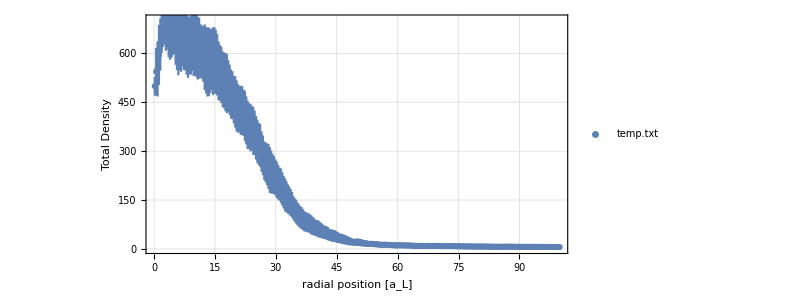

```mathematica
ErrorListPlot[datainput,GridLines->Automatic,ImageSize->600,Frame->True,FrameLabel->{"radial position [a_L]","Total Density"},LabelStyle->Directive[16,Bold,Black],AspectRatio->.5,PlotLegends->Placed[LineLegend[{fname},LabelStyle->18],{Right,Top}]]
```

### Fitting Via Lookup Table